```mathematica
(*CsPbBr3*)
```

```mathematica
h = 6.58*10^-16;
```

```mathematica
c = 3*10^14;
```

```mathematica
T = 2.309;
```

```mathematica
LT = 0.0063;
```

```mathematica
M = 0.214;
```

```mathematica
k[y_]:=(y+T)/(c*h)
```

```mathematica
b = 4.96;
```

```mathematica
EB=13.6 (*Hidrigen atm energy in eV *);
aB= 0.53*10^-4 (* in microns*);
```

```mathematica
κ[y_]:=b(1-LT/y)
```

```mathematica
SubMinus[γ][x_,y_] := (x^2-κ[y]*(k[y])^2)^(1/2)
```

```mathematica
(*Here I make the formula for the partial derivative of A*)
```

```mathematica
pA[x_,y_]:=1+(SubMinus[γ][x,y])/(b*(x^2-(k[y])^2)^(1/2))+y((-((b*LT)/y^2*(k[y])^2+κ[y]*(2k[y])/(c*h)))/(2*b*SubMinus[γ][x,y]*(x^2-(k[y])^2)^(1/2))+(SubMinus[γ][x,y]*k[y])/(b*c*h(x^2-(k[y])^2)*(x^2-(k[y])^2)^(1/2)))
```

```mathematica
(*Here I make the formula for the real part of the correction term*)
```

```mathematica
R[x_,y_] := (EB*aB^2)^(1/2)*(LT*x^2)/(b*(M*(LT-y))^(1/2)*(x^2-(k[y])^2)^(1/2))(*Real part of correction*)
```

```mathematica
(*Here I make the formula for the imaginary part of the correction term*)
```

```mathematica
H[x_,y_] := (-EB*(aB)^2*y*x^2)/(M(y(LT-y))^(1/2))(*Imaginary part of correction*)
```

```mathematica
(*Here I make the formula for the real part of the Delta term*)
```

```mathematica
DR[x_,y_] := -R[x,y]/pA[x,y] (*delta real*)
```

```mathematica
(*Here I make the formula for the imaginary part of the Delta term*)
```

```mathematica
DI[x_,y_]:=-H[x,y]/pA[x,y] (*delta imaginary*)
```

```mathematica
(*partial of energy with respect to momentum for infinite mass dispersion*)
```

```mathematica
pE[x_,y_]:= (2*x)/((2k[y])/(c*h)*κ[y]/(κ[y]+1)+((k[y])^2*b*LT)/(y^2(κ[y]+1)^2))
```

```mathematica
df=D[-R[x,y]/pA[x,y],x]; (*partial of the energy correction with respect to momentum*)
```

```mathematica
d[xVal_,yVal_]:=df/. {x->xVal,y->yVal} (*evaluating partial function*)
```

```mathematica
V[x_,y_] :=pE[x,y]+d[x,y] (*velocity of surface exciton polariton*)
```

```mathematica
j[x_]:=Solve[x^2==(k[y])^2*κ[y]/(κ[y]+1),y]
```

```mathematica
middleSolution[x_]:=y/.j[x][[2]]
```

```mathematica
qs1part1 = Range[11,13,0.1];
```

```mathematica
qs1part3 = Range[13,15,0.5];
```

```mathematica
qs1part2 = Range[15,60,0.75];
```

```mathematica
qs1 = Join[qs1part1,qs1part3,qs1part2]
```

{11.,11.1,11.2,11.3,11.4,11.5,11.6,11.7,11.8,11.9,12.,12.1,12.2,12.3,12.4,12.5,12.6,12.7,12.8,12.9,13.,13.,13.5,14.,14.5,15.,15.,15.75,16.5,17.25,18.,18.75,19.5,20.25,21.,21.75,22.5,23.25,24.,24.75,25.5,26.25,27.,27.75,28.5,29.25,30.,30.75,31.5,32.25,33.,33.75,34.5,35.25,36.,36.75,37.5,38.25,39.,39.75,40.5,41.25,42.,42.75,43.5,44.25,45.,45.75,46.5,47.25,48.,48.75,49.5,50.25,51.,51.75,52.5,53.25,54.,54.75,55.5,56.25,57.,57.75,58.5,59.25,60.}

```mathematica
qs1 = Append[qs1, 60];
```

```mathematica
yValues1=middleSolution/@qs1;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
xyPairs1=Transpose[{qs1,yValues1}]
```

{{11.,-0.00954062},{11.1,-0.0067152},{11.2,-0.00471322},{11.3,-0.00324227},{11.4,-0.00212534},{11.5,-0.00125284},{11.6,-0.000554746},{11.7,0.0000152432},{11.8,0.000488712},{11.9,0.000887831},{12.,0.00122856},{12.1,0.00152267},{12.2,0.00177897},{12.3,0.00200424},{12.4,0.00220372},{12.5,0.00238156},{12.6,0.00254105},{12.7,0.00268487},{12.8,0.00281519},{12.9,0.00293381},{13.,0.00304221},{13.,0.00304221},{13.5,0.00346875},{14.,0.00376609},{14.5,0.00398476},{15.,0.00415202},{15.,0.00415202},{15.75,0.00433981},{16.5,0.00447795},{17.25,0.00458352},{18.,0.0046666},{18.75,0.00473351},{19.5,0.00478844},{20.25,0.00483424},{21.,0.00487293},{21.75,0.00490599},{22.5,0.00493452},{23.25,0.00495934},{24.,0.00498111},{24.75,0.00500032},{25.5,0.00501738},{26.25,0.00503261},{27.,0.00504627},{27.75,0.00505859},{28.5,0.00506973},{29.25,0.00507985},{30.,0.00508908},{30.75,0.00509751},{31.5,0.00510524},{32.25,0.00511235},{33.,0.00511891},{33.75,0.00512497},{34.5,0.00513058},{35.25,0.00513579},{36.,0.00514064},{36.75,0.00514515},{37.5,0.00514937},{38.25,0.00515331},{39.,0.005157},{39.75,0.00516047},{40.5,0.00516372},{41.25,0.00516678},{42.,0.00516966},{42.75,0.00517238},{43.5,0.00517495},{44.25,0.00517738},{45.,0.00517967},{45.75,0.00518185},{46.5,0.00518392},{47.25,0.00518588},{48.,0.00518774},{48.75,0.00518951},{49.5,0.00519119},{50.25,0.0051928},{51.,0.00519433},{51.75,0.00519579},{52.5,0.00519719},{53.25,0.00519852},{54.,0.0051998},{54.75,0.00520102},{55.5,0.00520219},{56.25,0.00520331},{57.,0.00520438},{57.75,0.00520541},{58.5,0.0052064},{59.25,0.00520735},{60.,0.00520827},{60,0.00520827}}

```mathematica
realcorrection1 = DR @@@ xyPairs1
```

{0.+0.0000573746 ⅈ,0.+0.000065437 ⅈ,0.+0.0000731466 ⅈ,0.+0.0000799927 ⅈ,0.+0.0000849677 ⅈ,0.+0.0000857602 ⅈ,0.+0.0000757816 ⅈ,-0.0000168695,-0.000095173,-0.000127763,-0.000149664,-0.000165918,-0.000178601,-0.000188819,-0.000197243,-0.000204315,-0.000210339,-0.000215537,-0.000220071,-0.000224066,-0.000227619,-0.000227619,-0.000240933,-0.000250061,-0.000257215,-0.000263385,-0.000263385,-0.000271792,-0.000279816,-0.000287776,-0.000295807,-0.000303963,-0.000312262,-0.000320704,-0.000329283,-0.000337989,-0.000346812,-0.00035574,-0.000364764,-0.000373875,-0.000383065,-0.000392327,-0.000401654,-0.00041104,-0.00042048,-0.00042997,-0.000439505,-0.000449081,-0.000458696,-0.000468346,-0.000478029,-0.000487742,-0.000497484,-0.000507251,-0.000517043,-0.000526857,-0.000536692,-0.000546548,-0.000556421,-0.000566313,-0.00057622,-0.000586143,-0.000596081,-0.000606032,-0.000615996,-0.000625972,-0.00063596,-0.000645959,-0.000655968,-0.000665987,-0.000676015,-0.000686052,-0.000696098,-0.000706151,-0.000716213,-0.000726281,-0.000736357,-0.000746439,-0.000756528,-0.000766623,-0.000776723,-0.00078683,-0.000796941,-0.000807058,-0.00081718,-0.000827306,-0.000837437,-0.000837437}

```mathematica
actualReal1 = yValues1+realcorrection1;
```

```mathematica
group1=Transpose[{qs1,actualReal1}]
```

{{11.,-0.00954062+0.0000573746 ⅈ},{11.1,-0.0067152+0.000065437 ⅈ},{11.2,-0.00471322+0.0000731466 ⅈ},{11.3,-0.00324227+0.0000799927 ⅈ},{11.4,-0.00212534+0.0000849677 ⅈ},{11.5,-0.00125284+0.0000857602 ⅈ},{11.6,-0.000554746+0.0000757816 ⅈ},{11.7,-1.62629×10^-6},{11.8,0.000393539},{11.9,0.000760068},{12.,0.0010789},{12.1,0.00135675},{12.2,0.00160037},{12.3,0.00181542},{12.4,0.00200648},{12.5,0.00217724},{12.6,0.00233071},{12.7,0.00246933},{12.8,0.00259512},{12.9,0.00270974},{13.,0.0028146},{13.,0.0028146},{13.5,0.00322781},{14.,0.00351603},{14.5,0.00372755},{15.,0.00388864},{15.,0.00388864},{15.75,0.00406802},{16.5,0.00419813},{17.25,0.00429574},{18.,0.00437079},{18.75,0.00442955},{19.5,0.00447618},{20.25,0.00451354},{21.,0.00454365},{21.75,0.004568},{22.5,0.00458771},{23.25,0.0046036},{24.,0.00461634},{24.75,0.00462644},{25.5,0.00463431},{26.25,0.00464028},{27.,0.00464462},{27.75,0.00464755},{28.5,0.00464925},{29.25,0.00464988},{30.,0.00464957},{30.75,0.00464843},{31.5,0.00464655},{32.25,0.00464401},{33.,0.00464088},{33.75,0.00463723},{34.5,0.0046331},{35.25,0.00462854},{36.,0.0046236},{36.75,0.0046183},{37.5,0.00461268},{38.25,0.00460676},{39.,0.00460058},{39.75,0.00459415},{40.5,0.0045875},{41.25,0.00458064},{42.,0.00457358},{42.75,0.00456635},{43.5,0.00455895},{44.25,0.00455141},{45.,0.00454371},{45.75,0.00453589},{46.5,0.00452795},{47.25,0.00451989},{48.,0.00451172},{48.75,0.00450346},{49.5,0.0044951},{50.25,0.00448665},{51.,0.00447812},{51.75,0.00446951},{52.5,0.00446083},{53.25,0.00445208},{54.,0.00444327},{54.75,0.0044344},{55.5,0.00442546},{56.25,0.00441648},{57.,0.00440744},{57.75,0.00439836},{58.5,0.00438922},{59.25,0.00438005},{60.,0.00437083},{60,0.00437083}}

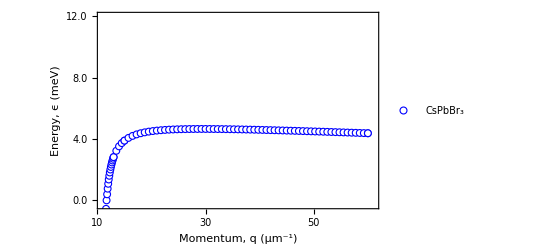

```mathematica
curr1= yValues1+Re[realcorrection1];
pair1 = Transpose[{qs1, curr1}];
s1 = ListPlot[pair1,  PlotMarkers->{Graphics[{EdgeForm[Blue],White,Disk[]}],7},FrameLabel -> {{Row[{"Energy, ",Style["ϵ",Italic]," (meV)"}],""}, {Row[{"Momentum, ",Style["q",Italic]," (μm^-1)"}],""}} ,Frame->True, FrameTicks->{{{{0,"0.0"},{0.002,"",{0.003,0}},{0.004,"4.0"},{0.006,"",{0.003,0}},{0.008,"8.0"},{0.01,"",{0.003,0}},{0.012,"12.0"}},{{0,"0.0"},{0.002,"",{0.003,0}},{0.004,"4.0"},{0.006,"",{0.003,0}},{0.008,"8.0"},{0.01,"",{0.003,0}},{0.012,"12.0"}, {0.0063,"ℏω_LT"}}},{{{10,"10"},{15,"",{0.003,0}},{20,"20"},{25,"", {0.003,0}},{30,"30"},{35,"",{0.003,0}},{40,"40"},{45,"", {0.003,0}},{50,"50"},{55,"",{0.003,0}},{60,"60"},{65,"",{0.003,0}},{70,"70"}},{{10,"10"},{15,"",{0.003,0}},{20,""},{25,"", {0.003,0}},{30,""},{35,"",{0.003,0}},{40,""},{45,"", {0.003,0}},{50,""},{55,"",{0.003,0}},{60,""},{65,"",{0.003,0}},{70,""}}}}, PlotRange->{{11,61},{-0.0003, 0.012}},PlotLegends->{"CsPbBr_3"}]
```

```mathematica
qs1 = Range[10.75,60,1];
yValues1 = middleSolution/@qs1;
xyPairs1= Transpose[{qs1,yValues1}];
realcorrection1 = DR @@@ xyPairs1;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
imaginarycorrection1= DI @@@ xyPairs1;
```

```mathematica
qandreal1 = Transpose[{qs1, realcorrection1}];
```

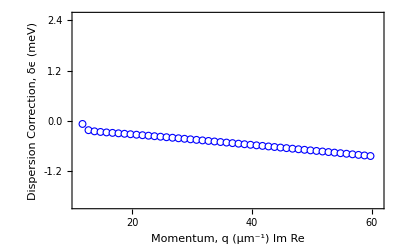

```mathematica
qversusreal1 = ListPlot[qandreal1, PlotMarkers->{Graphics[{EdgeForm[Blue],White,Disk[]}],7},FrameLabel -> {{"Dispersion Correction, δϵ (meV)",""}, {Row[{"Momentum, ",Style["q",Italic]," (μm^-1) Im Re"}],""}},Frame->True, FrameTicks->{{{{-0.0018,"",{0.003,0}},{-0.0012,"-1.2"},{-0.0006,"",{0.003,0}},{0,"0.0"},{0.0006,"",{0.003,0}},{0.0012,"1.2"},{0.0018,"",{0.003,0}},{0.0024,"2.4"}},{{-0.0018,"",{0.003,0}},{-0.0012,"-1.2"},{-0.0006,"",{0.003,0}},{0,"0.0"},{0.0006,"",{0.003,0}},{0.0012,"1.2"},{0.0018,"",{0.003,0}},{0.0024,"2.4"}}},{{{10,""},{15,"",{0.003,0}},{20,"20"},{25,"", {0.003,0}},{30,"30"},{35,"",{0.003,0}},{40,"40"},{45,"", {0.003,0}},{50,"50"},{55,"",{0.003,0}},{60,"60"},{65,"",{0.003,0}},{70,"70"}},{{10,""},{15,"",{0.003,0}},{20,""},{25,"", {0.003,0}},{30,""},{35,"",{0.003,0}},{40,""},{45,"", {0.003,0}},{50,""},{55,"",{0.003,0}},{60,""},{65,"",{0.003,0}},{70,""}}}}, PlotRange->{{11,61},{-0.002, 0.0025}}]
```

```mathematica
qandimaginary1= Transpose[{qs1, imaginarycorrection1}];
```

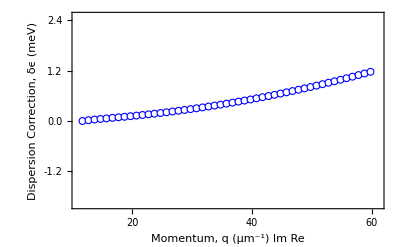

```mathematica
qversusimaginary1 = ListPlot[qandimaginary1, PlotMarkers->{Graphics[{EdgeForm[Blue],White,Disk[]}],7},FrameLabel -> {{"Dispersion Correction, δϵ (meV)",""}, {Row[{"Momentum, ",Style["q",Italic]," (μm^-1) Im Re"}],""}},Frame->True, FrameTicks->{{{{-0.0018,"",{0.003,0}},{-0.0012,"-1.2"},{-0.0006,"",{0.003,0}},{0,"0.0"},{0.0006,"",{0.003,0}},{0.0012,"1.2"},{0.0018,"",{0.003,0}},{0.0024,"2.4"}},{{-0.0018,"",{0.003,0}},{-0.0012,"-1.2"},{-0.0006,"",{0.003,0}},{0,"0.0"},{0.0006,"",{0.003,0}},{0.0012,"1.2"},{0.0018,"",{0.003,0}},{0.0024,"2.4"}}},{{{10,""},{15,"",{0.003,0}},{20,"20"},{25,"", {0.003,0}},{30,"30"},{35,"",{0.003,0}},{40,"40"},{45,"", {0.003,0}},{50,"50"},{55,"",{0.003,0}},{60,"60"},{65,"",{0.003,0}},{70,"70"}},{{10,""},{15,"",{0.003,0}},{20,""},{25,"", {0.003,0}},{30,""},{35,"",{0.003,0}},{40,""},{45,"", {0.003,0}},{50,""},{55,"",{0.003,0}},{60,""},{65,"",{0.003,0}},{70,""}}}}, PlotRange->{{11,61},{-0.002, 0.0025}}]
```

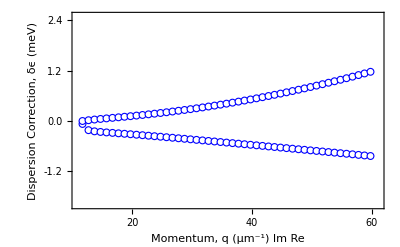

```mathematica
y1 = Show[qversusreal1, qversusimaginary1]
```

```mathematica
frontV1 = Range[0.01,8.9,0.25];
```

```mathematica
firstHalfV1 = Range[9,10,0.1];
```

```mathematica
middleV1 = Range[10,11,0.02];
```

```mathematica
thirdV1 = Range[11.1,12,0.1];
```

```mathematica
secondHalfV1 = Range[12, 27, 0.15];
```

```mathematica
qsV1 = Join[frontV1, firstHalfV1,middleV1, thirdV1,secondHalfV1];
```

```mathematica
yValuesforV1=middleSolution/@qsV1;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
xyPairsForV1=Transpose[{qsV1,yValuesforV1}];
```

```mathematica
Velocities1 = V @@@ xyPairsForV1;
```

```mathematica
VasFuncQ1 = Transpose[{qsV1, Re[Velocities1]/(c*h)}]
```

{{0.01,1.09593},{0.26,1.09592},{0.51,1.09591},{0.76,1.09589},{1.01,1.09588},{1.26,1.09586},{1.51,1.09584},{1.76,1.09582},{2.01,1.0958},{2.26,1.09578},{2.51,1.09575},{2.76,1.09573},{3.01,1.0957},{3.26,1.09566},{3.51,1.09563},{3.76,1.09559},{4.01,1.09554},{4.26,1.09549},{4.51,1.09543},{4.76,1.09537},{5.01,1.0953},{5.26,1.09521},{5.51,1.09512},{5.76,1.09501},{6.01,1.09488},{6.26,1.09473},{6.51,1.09455},{6.76,1.09434},{7.01,1.09408},{7.26,1.09377},{7.51,1.09338},{7.76,1.09288},{8.01,1.09225},{8.26,1.09141},{8.51,1.09027},{8.76,1.08868},{9.,1.08646},{9.1,1.08524},{9.2,1.08378},{9.3,1.08201},{9.4,1.07983},{9.5,1.07713},{9.6,1.0737},{9.7,1.0693},{9.8,1.0635},{9.9,1.0557},{10.,1.04489},{10.,1.04489},{10.02,1.04224},{10.04,1.0394},{10.06,1.03633},{10.08,1.03303},{10.1,1.02946},{10.12,1.0256},{10.14,1.02143},{10.16,1.0169},{10.18,1.01198},{10.2,1.00664},{10.22,1.00082},{10.24,0.994478},{10.26,0.987553},{10.28,0.979983},{10.3,0.971701},{10.32,0.962629},{10.34,0.952685},{10.36,0.941778},{10.38,0.929811},{10.4,0.916681},{10.42,0.902281},{10.44,0.886502},{10.46,0.869235},{10.48,0.850379},{10.5,0.829844},{10.52,0.807559},{10.54,0.783484},{10.56,0.757615},{10.58,0.729996},{10.6,0.700728},{10.62,0.669974},{10.64,0.63796},{10.66,0.604973},{10.68,0.571349},{10.7,0.53746},{10.72,0.503691},{10.74,0.470424},{10.76,0.438008},{10.78,0.406752},{10.8,0.376905},{10.82,0.348653},{10.84,0.32212},{10.86,0.297371},{10.88,0.274419},{10.9,0.253235},{10.92,0.23376},{10.94,0.215909},{10.96,0.199585},{10.98,0.184681},{11.,0.171088},{11.1,0.119154},{11.2,0.086087},{11.3,0.0644004},{11.4,0.0496671},{11.5,0.0393103},{11.6,0.0318022},{11.7,0.0254828},{11.8,0.02212},{11.9,0.0189012},{12.,0.0163085},{12.,0.0163085},{12.15,0.0132969},{12.3,0.0110374},{12.45,0.00930212},{12.6,0.0079418},{12.75,0.00685631},{12.9,0.00597661},{13.05,0.00525395},{13.2,0.00465314},{13.35,0.0041483},{13.5,0.00372005},{13.65,0.00335367},{13.8,0.00303779},{13.95,0.00276355},{14.1,0.00252394},{14.25,0.00231337},{14.4,0.00212733},{14.55,0.00196215},{14.7,0.00181482},{14.85,0.00168287},{15.,0.00156422},{15.15,0.00145715},{15.3,0.0013602},{15.45,0.00127212},{15.6,0.00119188},{15.75,0.00111856},{15.9,0.0010514},{16.05,0.00098972},{16.2,0.000932943},{16.35,0.000880563},{16.5,0.000832138},{16.65,0.000787279},{16.8,0.000745645},{16.95,0.000706935},{17.1,0.000670882},{17.25,0.000637247},{17.4,0.000605821},{17.55,0.000576413},{17.7,0.000548855},{17.85,0.000522996},{18.,0.000498698},{18.15,0.000475839},{18.3,0.000454308},{18.45,0.000434005},{18.6,0.000414837},{18.75,0.000396722},{18.9,0.000379585},{19.05,0.000363356},{19.2,0.000347973},{19.35,0.000333378},{19.5,0.000319519},{19.65,0.000306347},{19.8,0.000293818},{19.95,0.00028189},{20.1,0.000270526},{20.25,0.000259691},{20.4,0.000249354},{20.55,0.000239483},{20.7,0.000230052},{20.85,0.000221036},{21.,0.000212409},{21.15,0.000204151},{21.3,0.00019624},{21.45,0.000188658},{21.6,0.000181387},{21.75,0.00017441},{21.9,0.000167712},{22.05,0.000161278},{22.2,0.000155094},{22.35,0.000149148},{22.5,0.000143428},{22.65,0.000137922},{22.8,0.00013262},{22.95,0.000127513},{23.1,0.000122591},{23.25,0.000117845},{23.4,0.000113267},{23.55,0.000108849},{23.7,0.000104584},{23.85,0.000100465},{24.,0.0000964857},{24.15,0.0000926395},{24.3,0.0000889209},{24.45,0.0000853243},{24.6,0.0000818444},{24.75,0.0000784763},{24.9,0.0000752154},{25.05,0.0000720572},{25.2,0.0000689975},{25.35,0.0000660322},{25.5,0.0000631576},{25.65,0.0000603701},{25.8,0.0000576662},{25.95,0.0000550427},{26.1,0.0000524964},{26.25,0.0000500244},{26.4,0.0000476239},{26.55,0.0000452921},{26.7,0.0000430266},{26.85,0.0000408247},{27.,0.0000386844}}

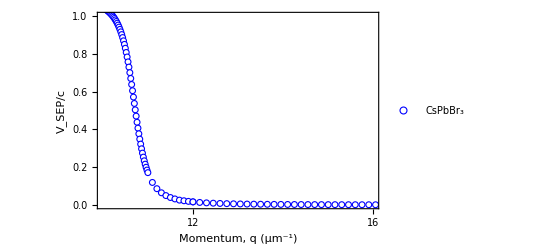

```mathematica
v1 = ListPlot[VasFuncQ1, PlotMarkers->{Graphics[{EdgeForm[Blue],White,Disk[]}],6},FrameLabel -> {{"V_SEP/c",""}, {Row[{"Momentum, ",Style["q",Italic]," (μm^-1)"}],""}} ,Frame->True,FrameTicks->{{{{0.0,"0.0"},{0.1,"",{0.003,0}},{0.2,"0.2"},{0.3,"",{0.003,0}},{0.4,"0.4"},{0.5,"",{0.003,0}},{0.6,"0.6"},{0.7,"",{0.003,0}},{0.8,"0.8"},{0.9,"",{0.003,0}},{1.0,"1.0"}},{{0.0,"0.0"},{0.1,"",{0.003,0}},{0.2,"0.2"},{0.3,"",{0.003,0}},{0.4,"0.4"},{0.5,"",{0.003,0}},{0.6,"0.6"},{0.7,"",{0.003,0}},{0.8,"0.8"},{0.9,"",{0.003,0}},{1.0,"1.0"}}},{{{8,"8"},{9,"",{0.003,0}},{10,"10"},{11,"", {0.003,0}},{12,"12"},{13,"",{0.003,0}},{14,"14"},{15,"", {0.003,0}},{16,"16"},{17,"",{0.003,0}},{18,"18"}},{{8,""},{9,"",{0.003,0}},{10,""},{11,"", {0.003,0}},{12,""},{13,"",{0.003,0}},{14,""},{15,"", {0.003,0}},{16,""},{17,"",{0.003,0}},{18,""}}}},PlotLegends->{"CsPbBr_3"},PlotRange->{{10,16},{0, 1}}]
```

```mathematica
(*CsPbCl3*)
```

```mathematica
T = 2.992;
LT = 0.0107;
M = 0.283;
k[y_]:=(y+T)/(c*h)
b = 4.07;
κ[y_]:=b(1-LT/y)
SubMinus[γ][x_,y_] := (x^2-κ[y]*(k[y])^2)^(1/2)
pA[x_,y_]:=1+(SubMinus[γ][x,y])/(b*(x^2-(k[y])^2)^(1/2))+y((-((b*LT)/y^2*(k[y])^2+κ[y]*(2k[y])/(c*h)))/(2*b*SubMinus[γ][x,y]*(x^2-(k[y])^2)^(1/2))+(SubMinus[γ][x,y]*k[y])/(b*c*h(x^2-(k[y])^2)*(x^2-(k[y])^2)^(1/2)))
R[x_,y_] := (EB*aB^2)^(1/2)*(LT*x^2)/(b*(M*(LT-y))^(1/2)*(x^2-(k[y])^2)^(1/2))(*Real part of correction*)

H[x_,y_] := (-EB*(aB)^2*y*x^2)/(M(y(LT-y))^(1/2))(*Imaginary part of correction*)

DR[x_,y_] := -R[x,y]/pA[x,y] (*delta real*)

DI[x_,y_]:=-H[x,y]/pA[x,y] (*delta imaginary*)

pE[x_,y_]:= (2*x)/((2k[y])/(c*h)*κ[y]/(κ[y]+1)+((k[y])^2*b*LT)/(y^2(κ[y]+1)^2))
df=D[-R[x,y]/pA[x,y],x];
d[xVal_,yVal_]:=df/. {x->xVal,y->yVal}
V[x_,y_] :=pE[x,y]+d[x,y]
j[x_]:=Solve[x^2==(k[y])^2*κ[y]/(κ[y]+1),y]
middleSolution[x_]:=y/.j[x][[2]]
```

```mathematica
qs2part1 = Range[13,18,0.10];
```

```mathematica
qs2part2  = Range[18, 60, 0.75];
```

```mathematica
qs2 = Join[qs2part1,qs2part2];
```

```mathematica
qs2 = Append[qs2, 60];
```

```mathematica
yValues2=middleSolution/@qs2;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
xyPairs2=Transpose[{qs2,yValues2}];
```

```mathematica
realcorrection2 = DR @@@ xyPairs2;
```

```mathematica
actualReal2 = yValues2+realcorrection2
```

{-0.147062+0.0000292625 ⅈ,-0.127871+0.0000319441 ⅈ,-0.109434+0.0000351072 ⅈ,-0.0920063+0.0000388654 ⅈ,-0.0759054+0.0000433404 ⅈ,-0.0614833+0.0000486373 ⅈ,-0.0490455+0.0000548021 ⅈ,-0.0387407+0.0000617864 ⅈ,-0.0304931+0.0000694474 ⅈ,-0.0240377+0.0000775926 ⅈ,-0.0190268+0.00008603 ⅈ,-0.0151254+0.0000945916 ⅈ,-0.0120565+0.000103128 ⅈ,-0.00960939+0.000111486 ⅈ,-0.00762889+0.000119476 ⅈ,-0.00600258+0.000126833 ⅈ,-0.00464874+0.000133151 ⅈ,-0.00350753+0.000137766 ⅈ,-0.00253459+0.000139539 ⅈ,-0.0016966+0.000136334 ⅈ,-0.000968207+0.000123534 ⅈ,-0.000329831+0.0000870936 ⅈ,0.000151891,0.000590042,0.000999765,0.00137444,0.00171631,0.00202867,0.00231477,0.00257757,0.00281964,0.00304325,0.00325035,0.00344264,0.00362163,0.0037886,0.00394469,0.00409092,0.00422815,0.00435719,0.00447872,0.00459337,0.00470168,0.00480416,0.00490126,0.00499336,0.00508085,0.00516405,0.00524325,0.00531874,0.00539075,0.00539075,0.00584016,0.00617229,0.00642631,0.00662573,0.00678551,0.00691561,0.00702294,0.00711241,0.00718763,0.0072513,0.00730549,0.0073518,0.0073915,0.0074256,0.00745492,0.00748012,0.00750175,0.00752028,0.00753608,0.00754948,0.00756076,0.00757016,0.00757787,0.00758407,0.00758891,0.00759253,0.00759504,0.00759654,0.00759714,0.0075969,0.00759589,0.00759419,0.00759185,0.00758891,0.00758543,0.00758145,0.007577,0.00757212,0.00756684,0.00756119,0.00755519,0.00754886,0.00754223,0.00753532,0.00752815,0.00752073,0.00751307,0.0075052,0.00749712,0.00748884,0.00748039,0.00747176,0.00746297,0.00745402,0.00744493,0.0074357,0.0074357}

```mathematica
group2=Transpose[{qs2,actualReal2}]
```

{{13.,-0.147062+0.0000292625 ⅈ},{13.1,-0.127871+0.0000319441 ⅈ},{13.2,-0.109434+0.0000351072 ⅈ},{13.3,-0.0920063+0.0000388654 ⅈ},{13.4,-0.0759054+0.0000433404 ⅈ},{13.5,-0.0614833+0.0000486373 ⅈ},{13.6,-0.0490455+0.0000548021 ⅈ},{13.7,-0.0387407+0.0000617864 ⅈ},{13.8,-0.0304931+0.0000694474 ⅈ},{13.9,-0.0240377+0.0000775926 ⅈ},{14.,-0.0190268+0.00008603 ⅈ},{14.1,-0.0151254+0.0000945916 ⅈ},{14.2,-0.0120565+0.000103128 ⅈ},{14.3,-0.00960939+0.000111486 ⅈ},{14.4,-0.00762889+0.000119476 ⅈ},{14.5,-0.00600258+0.000126833 ⅈ},{14.6,-0.00464874+0.000133151 ⅈ},{14.7,-0.00350753+0.000137766 ⅈ},{14.8,-0.00253459+0.000139539 ⅈ},{14.9,-0.0016966+0.000136334 ⅈ},{15.,-0.000968207+0.000123534 ⅈ},{15.1,-0.000329831+0.0000870936 ⅈ},{15.2,0.000151891},{15.3,0.000590042},{15.4,0.000999765},{15.5,0.00137444},{15.6,0.00171631},{15.7,0.00202867},{15.8,0.00231477},{15.9,0.00257757},{16.,0.00281964},{16.1,0.00304325},{16.2,0.00325035},{16.3,0.00344264},{16.4,0.00362163},{16.5,0.0037886},{16.6,0.00394469},{16.7,0.00409092},{16.8,0.00422815},{16.9,0.00435719},{17.,0.00447872},{17.1,0.00459337},{17.2,0.00470168},{17.3,0.00480416},{17.4,0.00490126},{17.5,0.00499336},{17.6,0.00508085},{17.7,0.00516405},{17.8,0.00524325},{17.9,0.00531874},{18.,0.00539075},{18.,0.00539075},{18.75,0.00584016},{19.5,0.00617229},{20.25,0.00642631},{21.,0.00662573},{21.75,0.00678551},{22.5,0.00691561},{23.25,0.00702294},{24.,0.00711241},{24.75,0.00718763},{25.5,0.0072513},{26.25,0.00730549},{27.,0.0073518},{27.75,0.0073915},{28.5,0.0074256},{29.25,0.00745492},{30.,0.00748012},{30.75,0.00750175},{31.5,0.00752028},{32.25,0.00753608},{33.,0.00754948},{33.75,0.00756076},{34.5,0.00757016},{35.25,0.00757787},{36.,0.00758407},{36.75,0.00758891},{37.5,0.00759253},{38.25,0.00759504},{39.,0.00759654},{39.75,0.00759714},{40.5,0.0075969},{41.25,0.00759589},{42.,0.00759419},{42.75,0.00759185},{43.5,0.00758891},{44.25,0.00758543},{45.,0.00758145},{45.75,0.007577},{46.5,0.00757212},{47.25,0.00756684},{48.,0.00756119},{48.75,0.00755519},{49.5,0.00754886},{50.25,0.00754223},{51.,0.00753532},{51.75,0.00752815},{52.5,0.00752073},{53.25,0.00751307},{54.,0.0075052},{54.75,0.00749712},{55.5,0.00748884},{56.25,0.00748039},{57.,0.00747176},{57.75,0.00746297},{58.5,0.00745402},{59.25,0.00744493},{60.,0.0074357},{60,0.0074357}}

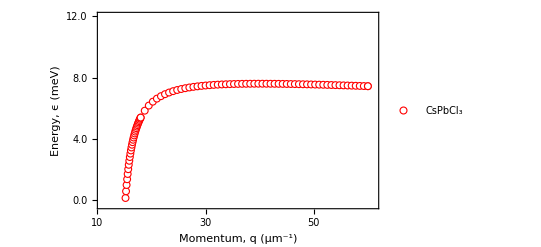

```mathematica
curr2= yValues2+realcorrection2;
pair2 = Transpose[{qs2, curr2}];
s2 = ListPlot[pair2,  PlotMarkers->{Graphics[{EdgeForm[Red],White,Disk[]}],7},FrameLabel -> {{Row[{"Energy, ",Style["ϵ",Italic]," (meV)"}],""}, {Row[{"Momentum, ",Style["q",Italic]," (μm^-1)"}],""}}  ,Frame->True, FrameTicks->{{{{0,"0.0"},{0.002,"",{0.003,0}},{0.004,"4.0"},{0.006,"",{0.003,0}},{0.008,"8.0"},{0.01,"",{0.003,0}},{0.012,"12.0"}},{{0,"0.0"},{0.002,"",{0.003,0}},{0.004,"4.0"},{0.006,"",{0.003,0}},{0.008,"8.0"},{0.01,"",{0.003,0}},{0.012,"12.0"}}},{{{10,"10"},{15,"",{0.003,0}},{20,"20"},{25,"", {0.003,0}},{30,"30"},{35,"",{0.003,0}},{40,"40"},{45,"", {0.003,0}},{50,"50"},{55,"",{0.003,0}},{60,"60"},{65,"",{0.003,0}},{70,"70"}},{{10,"10"},{15,"",{0.003,0}},{20,""},{25,"", {0.003,0}},{30,""},{35,"",{0.003,0}},{40,""},{45,"", {0.003,0}},{50,""},{55,"",{0.003,0}},{60,""},{65,"",{0.003,0}},{70,""}}}}, PlotRange->{{11,61},{-0.0003, 0.012}},PlotLegends->{"CsPbCl_3"}]
```

```mathematica
qs2= Range[10,60,0.75];
yValues2 = middleSolution/@qs2;
xyPairs2 = Transpose[{qs2,yValues2}];
realcorrection2 = DR @@@ xyPairs2;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
imaginarycorrection2= DI @@@ xyPairs2;
```

```mathematica
qandreal2 = Transpose[{qs2, realcorrection2}];
```

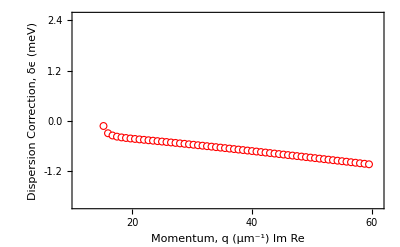

```mathematica
qversusreal2 = ListPlot[qandreal2, PlotMarkers->{Graphics[{EdgeForm[Red],White,Disk[]}],7},FrameLabel -> {{"Dispersion Correction, δϵ (meV)",""}, {Row[{"Momentum, ",Style["q",Italic]," (μm^-1) Im Re"}],""}},Frame->True, FrameTicks->{{{{-0.0018,"",{0.003,0}},{-0.0012,"-1.2"},{-0.0006,"",{0.003,0}},{0,"0.0"},{0.0006,"",{0.003,0}},{0.0012,"1.2"},{0.0018,"",{0.003,0}},{0.0024,"2.4"}},{{-0.0018,"",{0.003,0}},{-0.0012,"-1.2"},{-0.0006,"",{0.003,0}},{0,"0.0"},{0.0006,"",{0.003,0}},{0.0012,"1.2"},{0.0018,"",{0.003,0}},{0.0024,"2.4"}}},{{{10,""},{15,"",{0.003,0}},{20,"20"},{25,"", {0.003,0}},{30,"30"},{35,"",{0.003,0}},{40,"40"},{45,"", {0.003,0}},{50,"50"},{55,"",{0.003,0}},{60,"60"},{65,"",{0.003,0}},{70,"70"}},{{10,""},{15,"",{0.003,0}},{20,""},{25,"", {0.003,0}},{30,""},{35,"",{0.003,0}},{40,""},{45,"", {0.003,0}},{50,""},{55,"",{0.003,0}},{60,""},{65,"",{0.003,0}},{70,""}}}}, PlotRange->{{11,61},{-0.002, 0.0025}}]
```

```mathematica
qandimaginary2= Transpose[{qs2, imaginarycorrection2}];
```

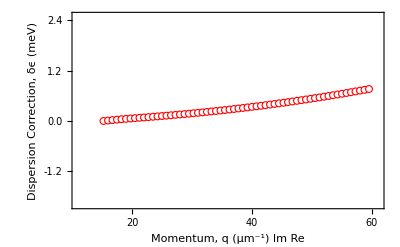

```mathematica
qversusimaginary2 = ListPlot[qandimaginary2, PlotMarkers->{Graphics[{EdgeForm[Red],White,Disk[]}],7},FrameLabel -> {{"Dispersion Correction, δϵ (meV)",""}, {Row[{"Momentum, ",Style["q",Italic]," (μm^-1) Im Re"}],""}},Frame->True, FrameTicks->{{{{-0.0018,"",{0.003,0}},{-0.0012,"-1.2"},{-0.0006,"",{0.003,0}},{0,"0.0"},{0.0006,"",{0.003,0}},{0.0012,"1.2"},{0.0018,"",{0.003,0}},{0.0024,"2.4"}},{{-0.0018,"",{0.003,0}},{-0.0012,"-1.2"},{-0.0006,"",{0.003,0}},{0,"0.0"},{0.0006,"",{0.003,0}},{0.0012,"1.2"},{0.0018,"",{0.003,0}},{0.0024,"2.4"}}},{{{10,""},{15,"",{0.003,0}},{20,"20"},{25,"", {0.003,0}},{30,"30"},{35,"",{0.003,0}},{40,"40"},{45,"", {0.003,0}},{50,"50"},{55,"",{0.003,0}},{60,"60"},{65,"",{0.003,0}},{70,"70"}},{{10,""},{15,"",{0.003,0}},{20,""},{25,"", {0.003,0}},{30,""},{35,"",{0.003,0}},{40,""},{45,"", {0.003,0}},{50,""},{55,"",{0.003,0}},{60,""},{65,"",{0.003,0}},{70,""}}}}, PlotRange->{{11,61},{-0.002, 0.0025}}]
```

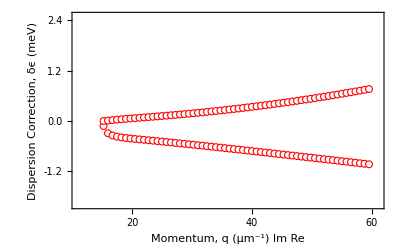

```mathematica
y2 = Show[qversusreal2, qversusimaginary2]
```

```mathematica
frontV2 = Range[0.01,10,0.25];
```

```mathematica
firstHalfV2 = Range[10,13,0.1];
```

```mathematica
middleV2 = Range[13,14,0.02];
```

```mathematica
thirdV2 = Range[14,17,0.1];
```

```mathematica
secondHalfV2= Range[17, 27, 0.15];
```

```mathematica
qsV2 = Join[frontV2, firstHalfV2,middleV2, thirdV2,secondHalfV2];
```

```mathematica
yValuesforV2=middleSolution/@qsV2;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
xyPairsForV2=Transpose[{qsV2,yValuesforV2}];
```

```mathematica
Velocities2 = V @@@ xyPairsForV2;
```

```mathematica
VasFuncQ2 = Transpose[{qsV2, Re[Velocities2]/(c*h)}]
```

{{0.01,1.11572},{0.26,1.1157},{0.51,1.11569},{0.76,1.11567},{1.01,1.11565},{1.26,1.11563},{1.51,1.11561},{1.76,1.11559},{2.01,1.11557},{2.26,1.11555},{2.51,1.11552},{2.76,1.11549},{3.01,1.11546},{3.26,1.11543},{3.51,1.1154},{3.76,1.11536},{4.01,1.11532},{4.26,1.11528},{4.51,1.11523},{4.76,1.11518},{5.01,1.11513},{5.26,1.11507},{5.51,1.115},{5.76,1.11493},{6.01,1.11486},{6.26,1.11477},{6.51,1.11467},{6.76,1.11457},{7.01,1.11445},{7.26,1.11432},{7.51,1.11417},{7.76,1.114},{8.01,1.11381},{8.26,1.11359},{8.51,1.11334},{8.76,1.11305},{9.01,1.11271},{9.26,1.11231},{9.51,1.11184},{9.76,1.11128},{10.,1.11063},{10.1,1.11031},{10.2,1.10998},{10.3,1.10961},{10.4,1.1092},{10.5,1.10876},{10.6,1.10828},{10.7,1.10774},{10.8,1.10715},{10.9,1.1065},{11.,1.10577},{11.1,1.10496},{11.2,1.10405},{11.3,1.10302},{11.4,1.10186},{11.5,1.10054},{11.6,1.09903},{11.7,1.09729},{11.8,1.09528},{11.9,1.09293},{12.,1.09018},{12.1,1.08692},{12.2,1.08303},{12.3,1.07833},{12.4,1.0726},{12.5,1.06554},{12.6,1.05672},{12.7,1.04554},{12.8,1.0312},{12.9,1.01251},{13.,0.98785},{13.,0.98785},{13.02,0.982014},{13.04,0.975828},{13.06,0.969271},{13.08,0.96232},{13.1,0.954948},{13.12,0.94713},{13.14,0.93884},{13.16,0.93005},{13.18,0.920731},{13.2,0.910856},{13.22,0.900396},{13.24,0.889324},{13.26,0.877614},{13.28,0.865239},{13.3,0.852179},{13.32,0.838413},{13.34,0.823927},{13.36,0.808711},{13.38,0.792761},{13.4,0.776081},{13.42,0.758681},{13.44,0.740582},{13.46,0.721814},{13.48,0.702419},{13.5,0.682446},{13.52,0.661957},{13.54,0.641023},{13.56,0.619725},{13.58,0.598151},{13.6,0.576394},{13.62,0.554553},{13.64,0.532728},{13.66,0.511018},{13.68,0.489521},{13.7,0.468329},{13.72,0.447528},{13.74,0.427195},{13.76,0.407399},{13.78,0.388197},{13.8,0.369637},{13.82,0.351756},{13.84,0.334582},{13.86,0.318131},{13.88,0.302413},{13.9,0.287429},{13.92,0.273172},{13.94,0.259631},{13.96,0.24679},{13.98,0.234628},{14.,0.223122},{14.,0.223122},{14.1,0.174502},{14.2,0.138193},{14.3,0.111042},{14.4,0.0905557},{14.5,0.0749003},{14.6,0.0627668},{14.7,0.0532282},{14.8,0.045626},{14.9,0.0394886},{15.,0.0344743},{15.1,0.0303323},{15.2,0.0267659},{15.3,0.0240952},{15.4,0.0217093},{15.5,0.0196374},{15.6,0.017837},{15.7,0.0162663},{15.8,0.0148894},{15.9,0.0136766},{16.,0.0126034},{16.1,0.0116495},{16.2,0.0107981},{16.3,0.0100351},{16.4,0.00934896},{16.5,0.00872965},{16.6,0.00816888},{16.7,0.00765953},{16.8,0.00719555},{16.9,0.00677174},{17.,0.00638361},{17.,0.00638361},{17.15,0.00585997},{17.3,0.005397},{17.45,0.0049857},{17.6,0.00461868},{17.75,0.00428983},{17.9,0.00399404},{18.05,0.00372705},{18.2,0.00348522},{18.35,0.00326552},{18.5,0.00306532},{18.65,0.00288238},{18.8,0.00271478},{18.95,0.00256086},{19.1,0.00241917},{19.25,0.00228844},{19.4,0.00216758},{19.55,0.00205563},{19.7,0.00195172},{19.85,0.00185511},{20.,0.00176513},{20.15,0.00168119},{20.3,0.00160275},{20.45,0.00152936},{20.6,0.00146059},{20.75,0.00139606},{20.9,0.00133542},{21.05,0.00127838},{21.2,0.00122465},{21.35,0.00117398},{21.5,0.00112615},{21.65,0.00108094},{21.8,0.00103818},{21.95,0.000997684},{22.1,0.000959298},{22.25,0.000922879},{22.4,0.000888294},{22.55,0.000855425},{22.7,0.000824158},{22.85,0.000794393},{23.,0.000766034},{23.15,0.000738996},{23.3,0.000713197},{23.45,0.000688564},{23.6,0.000665026},{23.75,0.000642522},{23.9,0.000620991},{24.05,0.000600379},{24.2,0.000580633},{24.35,0.000561707},{24.5,0.000543556},{24.65,0.000526139},{24.8,0.000509416},{24.95,0.000493351},{25.1,0.000477912},{25.25,0.000463065},{25.4,0.000448781},{25.55,0.000435032},{25.7,0.000421792},{25.85,0.000409036},{26.,0.000396741},{26.15,0.000384886},{26.3,0.00037345},{26.45,0.000362413},{26.6,0.000351757},{26.75,0.000341465},{26.9,0.000331521}}

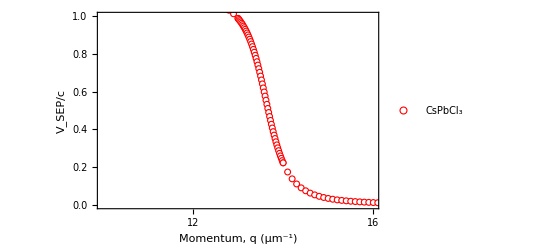

```mathematica
v2 = ListPlot[VasFuncQ2, PlotMarkers->{Graphics[{EdgeForm[Red],White,Disk[]}],6},FrameLabel -> {{"V_SEP/c",""}, {Row[{"Momentum, ",Style["q",Italic]," (μm^-1)"}],""}} ,Frame->True,FrameTicks->{{{{0.0,"0.0"},{0.1,"",{0.003,0}},{0.2,"0.2"},{0.3,"",{0.003,0}},{0.4,"0.4"},{0.5,"",{0.003,0}},{0.6,"0.6"},{0.7,"",{0.003,0}},{0.8,"0.8"},{0.9,"",{0.003,0}},{1.0,"1.0"}},{{0.0,"0.0"},{0.1,"",{0.003,0}},{0.2,"0.2"},{0.3,"",{0.003,0}},{0.4,"0.4"},{0.5,"",{0.003,0}},{0.6,"0.6"},{0.7,"",{0.003,0}},{0.8,"0.8"},{0.9,"",{0.003,0}},{1.0,"1.0"}}},{{{8,"8"},{9,"",{0.003,0}},{10,"10"},{11,"", {0.003,0}},{12,"12"},{13,"",{0.003,0}},{14,"14"},{15,"", {0.003,0}},{16,"16"},{17,"",{0.003,0}},{18,"18"}},{{8,""},{9,"",{0.003,0}},{10,""},{11,"", {0.003,0}},{12,""},{13,"",{0.003,0}},{14,""},{15,"", {0.003,0}},{16,""},{17,"",{0.003,0}},{18,""}}}},PlotLegends->{"CsPbCl_3"},PlotRange->{{10,16},{0,1}}]
```

```mathematica
T = (2.992+2.309)/2;
```

```mathematica
LT = (0.0107+0.0063)/2;
```

```mathematica
M = (0.283+0.214)/2;
```

```mathematica
k[y_]:=(y+T)/(c*h)
```

```mathematica
b = (4.07+4.96)/2;
```

```mathematica
κ[y_]:=b(1-LT/y)
```

```mathematica
SubMinus[γ][x_,y_] := (x^2-κ[y]*(k[y])^2)^(1/2)
```

```mathematica
pA[x_,y_]:=1+(SubMinus[γ][x,y])/(b*(x^2-(k[y])^2)^(1/2))+y((-((b*LT)/y^2*(k[y])^2+κ[y]*(2k[y])/(c*h)))/(2*b*SubMinus[γ][x,y]*(x^2-(k[y])^2)^(1/2))+(SubMinus[γ][x,y]*k[y])/(b*c*h(x^2-(k[y])^2)*(x^2-(k[y])^2)^(1/2)))
```

```mathematica
R[x_,y_] := (EB*aB^2)^(1/2)*(LT*x^2)/(b*(M*(LT-y))^(1/2)*(x^2-(k[y])^2)^(1/2))(*Real part of correction*)

H[x_,y_] := (-EB*(aB)^2*y*x^2)/(M(y(LT-y))^(1/2))(*Imaginary part of correction*)

DR[x_,y_] := -R[x,y]/pA[x,y] (*delta real*)

DI[x_,y_]:=-H[x,y]/pA[x,y] (*delta imaginary*)

pE[x_,y_]:= (2*x)/((2k[y])/(c*h)*κ[y]/(κ[y]+1)+((k[y])^2*b*LT)/(y^2(κ[y]+1)^2))
df=D[-R[x,y]/pA[x,y],x];
d[xVal_,yVal_]:=df/. {x->xVal,y->yVal}
```

```mathematica
V[x_,y_] :=pE[x,y]+d[x,y]
j[x_]:=Solve[x^2==(k[y])^2*κ[y]/(κ[y]+1),y]
middleSolution[x_]:=y/.j[x][[2]]
```

```mathematica
qs3part1 = Range[12.95,14.7,0.10];
```

```mathematica
qs3part3 = Range[14.7,16.4,0.35];
```

```mathematica
qs3part2 = Range[16.5,60,0.75];
```

```mathematica
qs3  = Join[qs3part1,qs3part3, qs3part2];
```

```mathematica
qs3 = Append[qs3, 60];
```

```mathematica
yValues3=middleSolution/@qs3;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
xyPairs3=Transpose[{qs3,yValues3}];
```

```mathematica
realcorrection3 = DR @@@ xyPairs3;
```

```mathematica
actualReal3 = yValues3+realcorrection3;
```

```mathematica
group3=Transpose[{qs3,actualReal3}]
```

{{12.95,-0.0040716+0.000104888 ⅈ},{13.05,-0.00289757+0.000109886 ⅈ},{13.15,-0.00193438+0.000111584 ⅈ},{13.25,-0.00113183+0.000106563 ⅈ},{13.35,-0.000454004+0.0000850323 ⅈ},{13.45,0.0000714722},{13.55,0.000505766},{13.65,0.000906227},{13.75,0.00126437},{13.85,0.00158449},{13.95,0.00187158},{14.05,0.00213013},{14.15,0.00236399},{14.25,0.0025764},{14.35,0.00277011},{14.45,0.0029474},{14.55,0.00311024},{14.65,0.00326028},{14.7,0.00333095},{15.05,0.00375805},{15.4,0.00409342},{15.75,0.00436323},{16.1,0.00458461},{16.5,0.00479309},{17.25,0.00509317},{18.,0.00531292},{18.75,0.00547952},{19.5,0.00560916},{20.25,0.00571207},{21.,0.00579503},{21.75,0.00586273},{22.5,0.00591849},{23.25,0.00596474},{24.,0.00600331},{24.75,0.00603558},{25.5,0.00606263},{26.25,0.0060853},{27.,0.00610426},{27.75,0.00612007},{28.5,0.00613316},{29.25,0.0061439},{30.,0.0061526},{30.75,0.00615951},{31.5,0.00616485},{32.25,0.0061688},{33.,0.00617151},{33.75,0.00617312},{34.5,0.00617374},{35.25,0.00617348},{36.,0.00617242},{36.75,0.00617064},{37.5,0.0061682},{38.25,0.00616517},{39.,0.0061616},{39.75,0.00615753},{40.5,0.00615302},{41.25,0.00614808},{42.,0.00614276},{42.75,0.00613709},{43.5,0.0061311},{44.25,0.0061248},{45.,0.00611823},{45.75,0.0061114},{46.5,0.00610432},{47.25,0.00609703},{48.,0.00608952},{48.75,0.00608182},{49.5,0.00607394},{50.25,0.00606589},{51.,0.00605767},{51.75,0.00604931},{52.5,0.00604081},{53.25,0.00603218},{54.,0.00602342},{54.75,0.00601455},{55.5,0.00600556},{56.25,0.00599647},{57.,0.00598728},{57.75,0.005978},{58.5,0.00596864},{59.25,0.00595918},{60.,0.00594965},{60,0.00594965}}

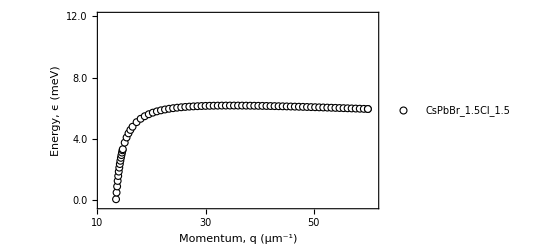

```mathematica
curr3= yValues3+realcorrection3;
pair3 = Transpose[{qs3, curr3}];
s3 = ListPlot[pair3,  PlotMarkers->{Graphics[{EdgeForm[Black],White,Disk[]}],7},FrameLabel -> {{Row[{"Energy, ",Style["ϵ",Italic]," (meV)"}],""}, {Row[{"Momentum, ",Style["q",Italic]," (μm^-1)"}],""}} ,Frame->True, FrameTicks->{{{{0,"0.0"},{0.002,"",{0.003,0}},{0.004,"4.0"},{0.006,"",{0.003,0}},{0.008,"8.0"},{0.01,"",{0.003,0}},{0.012,"12.0"}},{{0,"0.0"},{0.002,"",{0.003,0}},{0.004,"4.0"},{0.006,"",{0.003,0}},{0.008,"8.0"},{0.01,"",{0.003,0}},{0.012,"12.0"}}},{{{10,"10"},{15,"",{0.003,0}},{20,"20"},{25,"", {0.003,0}},{30,"30"},{35,"",{0.003,0}},{40,"40"},{45,"", {0.003,0}},{50,"50"},{55,"",{0.003,0}},{60,"60"},{65,"",{0.003,0}},{70,"70"}},{{10,"10"},{15,"",{0.003,0}},{20,""},{25,"", {0.003,0}},{30,""},{35,"",{0.003,0}},{40,""},{45,"", {0.003,0}},{50,""},{55,"",{0.003,0}},{60,""},{65,"",{0.003,0}},{70,""}}}}, PlotRange->{{11,61},{-0.0003, 0.012}},PlotLegends->{"CsPbBr_1.5Cl_1.5"}]
```

```mathematica
qs3 = Range[10.75,60,1];
```

```mathematica
yValues3 = middleSolution/@qs3;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
xyPairs3 = Transpose[{qs3,yValues3}];
```

```mathematica
realcorrection3 = DR @@@ xyPairs3;
```

```mathematica
imaginarycorrection3= DI @@@ xyPairs3;
```

```mathematica
qandreal3 = Transpose[{qs3, realcorrection3}];
```

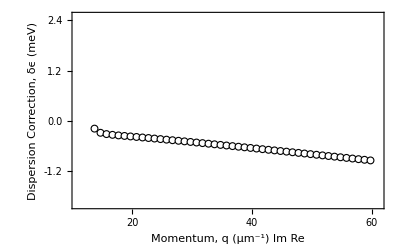

```mathematica
qversusreal3 = ListPlot[qandreal3, PlotMarkers->{Graphics[{EdgeForm[Black],White,Disk[]}],7},FrameLabel -> {{"Dispersion Correction, δϵ (meV)",""}, {Row[{"Momentum, ",Style["q",Italic]," (μm^-1) Im Re"}],""}},Frame->True, FrameTicks->{{{{-0.0018,"",{0.003,0}},{-0.0012,"-1.2"},{-0.0006,"",{0.003,0}},{0,"0.0"},{0.0006,"",{0.003,0}},{0.0012,"1.2"},{0.0018,"",{0.003,0}},{0.0024,"2.4"}},{{-0.0018,"",{0.003,0}},{-0.0012,"-1.2"},{-0.0006,"",{0.003,0}},{0,"0.0"},{0.0006,"",{0.003,0}},{0.0012,"1.2"},{0.0018,"",{0.003,0}},{0.0024,"2.4"}}},{{{10,""},{15,"",{0.003,0}},{20,"20"},{25,"", {0.003,0}},{30,"30"},{35,"",{0.003,0}},{40,"40"},{45,"", {0.003,0}},{50,"50"},{55,"",{0.003,0}},{60,"60"},{65,"",{0.003,0}},{70,"70"}},{{10,""},{15,"",{0.003,0}},{20,""},{25,"", {0.003,0}},{30,""},{35,"",{0.003,0}},{40,""},{45,"", {0.003,0}},{50,""},{55,"",{0.003,0}},{60,""},{65,"",{0.003,0}},{70,""}}}}, PlotRange->{{11,61},{-0.002, 0.0025}}]
```

```mathematica
qandimaginary3= Transpose[{qs3, imaginarycorrection3}];
```

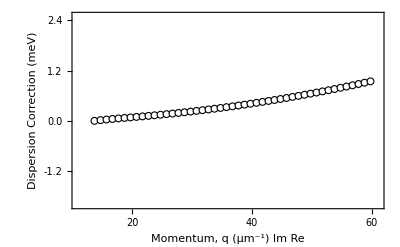

```mathematica
qversusimaginary3 = ListPlot[qandimaginary3, PlotMarkers->{Graphics[{EdgeForm[Black],White,Disk[]}],7},FrameLabel -> {{"Dispersion Correction (meV)",""}, {Row[{"Momentum, ",Style["q",Italic]," (μm^-1) Im Re"}],""}},Frame->True, FrameTicks->{{{{-0.0018,"",{0.003,0}},{-0.0012,"-1.2"},{-0.0006,"",{0.003,0}},{0,"0.0"},{0.0006,"",{0.003,0}},{0.0012,"1.2"},{0.0018,"",{0.003,0}},{0.0024,"2.4"}},{{-0.0018,"",{0.003,0}},{-0.0012,"-1.2"},{-0.0006,"",{0.003,0}},{0,"0.0"},{0.0006,"",{0.003,0}},{0.0012,"1.2"},{0.0018,"",{0.003,0}},{0.0024,"2.4"}}},{{{10,""},{15,"",{0.003,0}},{20,"20"},{25,"", {0.003,0}},{30,"30"},{35,"",{0.003,0}},{40,"40"},{45,"", {0.003,0}},{50,"50"},{55,"",{0.003,0}},{60,"60"},{65,"",{0.003,0}},{70,"70"}},{{10,""},{15,"",{0.003,0}},{20,""},{25,"", {0.003,0}},{30,""},{35,"",{0.003,0}},{40,""},{45,"", {0.003,0}},{50,""},{55,"",{0.003,0}},{60,""},{65,"",{0.003,0}},{70,""}}}}, PlotRange->{{11,61},{-0.002, 0.0025}}]
```

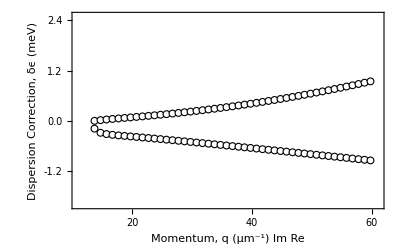

```mathematica
y3 = Show[qversusreal3, qversusimaginary3]
```

```mathematica
frontV3 = Range[0.01,11,0.25];
```

```mathematica
firstHalfV3 = Range[10.8,11.8,0.1];
```

```mathematica
middleV3 = Range[11.8,12.7,0.015];
```

```mathematica
thirdV3 = Range[12.7,14,0.09];
```

```mathematica
secondHalfV3= Range[14, 27, 0.15];
```

```mathematica
qsV3 = Join[frontV3, firstHalfV3,middleV3, thirdV3,secondHalfV3];
```

```mathematica
yValuesforV3=middleSolution/@qsV3;
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
xyPairsForV3=Transpose[{qsV3,yValuesforV3}];
```

```mathematica
Velocities3 = V @@@ xyPairsForV3;
```

```mathematica
VasFuncQ3 = Transpose[{qsV3, Re[Velocities3]/(c*h)}]
```

{{0.01,1.10489},{0.26,1.10487},{0.51,1.10486},{0.76,1.10484},{1.01,1.10483},{1.26,1.10481},{1.51,1.10479},{1.76,1.10477},{2.01,1.10475},{2.26,1.10472},{2.51,1.1047},{2.76,1.10467},{3.01,1.10464},{3.26,1.10461},{3.51,1.10458},{3.76,1.10454},{4.01,1.1045},{4.26,1.10445},{4.51,1.1044},{4.76,1.10435},{5.01,1.10428},{5.26,1.10422},{5.51,1.10414},{5.76,1.10406},{6.01,1.10396},{6.26,1.10386},{6.51,1.10373},{6.76,1.1036},{7.01,1.10344},{7.26,1.10325},{7.51,1.10304},{7.76,1.10279},{8.01,1.10249},{8.26,1.10214},{8.51,1.10171},{8.76,1.10118},{9.01,1.10053},{9.26,1.09971},{9.51,1.09865},{9.76,1.09726},{10.01,1.09537},{10.26,1.09273},{10.51,1.08889},{10.76,1.083},{10.8,1.08178},{10.9,1.07825},{11.,1.07388},{11.1,1.06839},{11.2,1.06141},{11.3,1.05234},{11.4,1.04035},{11.5,1.02415},{11.6,1.0018},{11.7,0.970315},{11.8,0.92532},{11.8,0.92532},{11.815,0.917058},{11.83,0.908341},{11.845,0.899144},{11.86,0.889448},{11.875,0.87923},{11.89,0.86847},{11.905,0.857148},{11.92,0.845248},{11.935,0.832753},{11.95,0.819652},{11.965,0.805937},{11.98,0.791602},{11.995,0.776647},{12.01,0.76108},{12.025,0.744912},{12.04,0.728162},{12.055,0.710856},{12.07,0.693027},{12.085,0.674717},{12.1,0.655974},{12.115,0.636854},{12.13,0.617419},{12.145,0.597738},{12.16,0.577881},{12.175,0.557926},{12.19,0.53795},{12.205,0.518031},{12.22,0.498247},{12.235,0.47867},{12.25,0.459373},{12.265,0.440421},{12.28,0.421872},{12.295,0.40378},{12.31,0.386188},{12.325,0.369136},{12.34,0.352653},{12.355,0.336761},{12.37,0.321477},{12.385,0.306809},{12.4,0.292761},{12.415,0.279332},{12.43,0.266513},{12.445,0.254296},{12.46,0.242665},{12.475,0.231606},{12.49,0.2211},{12.505,0.211126},{12.52,0.201664},{12.535,0.192692},{12.55,0.184189},{12.565,0.176132},{12.58,0.168498},{12.595,0.161268},{12.61,0.154419},{12.625,0.147932},{12.64,0.141786},{12.655,0.135962},{12.67,0.130444},{12.685,0.125212},{12.7,0.120252},{12.7,0.120252},{12.79,0.0953648},{12.88,0.0769773},{12.97,0.0631587},{13.06,0.0525905},{13.15,0.0443706},{13.24,0.0378759},{13.33,0.0326696},{13.42,0.0284408},{13.51,0.0250443},{13.6,0.0222867},{13.69,0.0199213},{13.78,0.017898},{13.87,0.0161596},{13.96,0.0146571},{14.,0.0140544},{14.15,0.0120911},{14.3,0.0105065},{14.45,0.00921009},{14.6,0.00813649},{14.75,0.00723774},{14.9,0.00647801},{15.05,0.00583016},{15.2,0.00527332},{15.35,0.00479126},{15.5,0.0043712},{15.65,0.00400297},{15.8,0.00367839},{15.95,0.00339083},{16.1,0.00313489},{16.25,0.00290609},{16.4,0.00270074},{16.55,0.00251573},{16.7,0.00234848},{16.85,0.00219678},{17.,0.00205876},{17.15,0.00193283},{17.3,0.00181762},{17.45,0.00171194},{17.6,0.00161478},{17.75,0.00152524},{17.9,0.00144254},{18.05,0.00136602},{18.2,0.00129506},{18.35,0.00122915},{18.5,0.00116781},{18.65,0.00111064},{18.8,0.00105726},{18.95,0.00100735},{19.1,0.000960608},{19.25,0.000916781},{19.4,0.000875628},{19.55,0.000836937},{19.7,0.000800515},{19.85,0.00076619},{20.,0.000733803},{20.15,0.000703211},{20.3,0.000674286},{20.45,0.000646908},{20.6,0.000620969},{20.75,0.00059637},{20.9,0.000573022},{21.05,0.00055084},{21.2,0.000529749},{21.35,0.000509679},{21.5,0.000490566},{21.65,0.000472348},{21.8,0.000454973},{21.95,0.000438388},{22.1,0.000422548},{22.25,0.000407407},{22.4,0.000392926},{22.55,0.000379068},{22.7,0.000365797},{22.85,0.00035308},{23.,0.000340888},{23.15,0.000329192},{23.3,0.000317966},{23.45,0.000307185},{23.6,0.000296826},{23.75,0.000286868},{23.9,0.00027729},{24.05,0.000268073},{24.2,0.000259199},{24.35,0.000250653},{24.5,0.000242417},{24.65,0.000234478},{24.8,0.00022682},{24.95,0.000219433},{25.1,0.000212301},{25.25,0.000205416},{25.4,0.000198764},{25.55,0.000192336},{25.7,0.000186122},{25.85,0.000180112},{26.,0.000174299},{26.15,0.000168673},{26.3,0.000163227},{26.45,0.000157952},{26.6,0.000152843},{26.75,0.000147892},{26.9,0.000143093}}

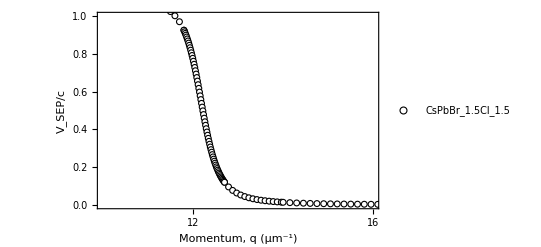

```mathematica
v3 = ListPlot[VasFuncQ3, PlotMarkers->{Graphics[{EdgeForm[Black],White,Disk[]}],6},FrameLabel -> {{"V_SEP/c",""}, {Row[{"Momentum, ",Style["q",Italic]," (μm^-1)"}],""}} ,Frame->True,FrameTicks->{{{{0.0,"0.0"},{0.1,"",{0.003,0}},{0.2,"0.2"},{0.3,"",{0.003,0}},{0.4,"0.4"},{0.5,"",{0.003,0}},{0.6,"0.6"},{0.7,"",{0.003,0}},{0.8,"0.8"},{0.9,"",{0.003,0}},{1.0,"1.0"}},{{0.0,"0.0"},{0.1,"",{0.003,0}},{0.2,"0.2"},{0.3,"",{0.003,0}},{0.4,"0.4"},{0.5,"",{0.003,0}},{0.6,"0.6"},{0.7,"",{0.003,0}},{0.8,"0.8"},{0.9,"",{0.003,0}},{1.0,"1.0"}}},{{{8,"8"},{9,"",{0.003,0}},{10,"10"},{11,"", {0.003,0}},{12,"12"},{13,"",{0.003,0}},{14,"14"},{15,"", {0.003,0}},{16,"16"},{17,"",{0.003,0}},{18,"18"}},{{8,""},{9,"",{0.003,0}},{10,""},{11,"", {0.003,0}},{12,""},{13,"",{0.003,0}},{14,""},{15,"", {0.003,0}},{16,""},{17,"",{0.003,0}},{18,""}}}},PlotLegends->{"CsPbBr_1.5Cl_1.5"},PlotRange->{{10,16},{0,1}}]
```

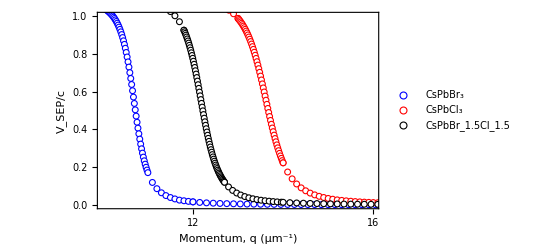

```mathematica
FinalVelocities = Show[v1,v2,v3]
```

```mathematica
BrLT = ContourPlot[y==0.0063,{x,11,61},{y,-0.0003, 0.011}, PlotRange->{{11,61},{-0.0003, 0.012}}, ContourStyle->{Dashed, ColorData["DeepSeaColors"][0.2]}]
```

```mathematica
ClLT = ContourPlot[y==0.0107,{x,11,61},{y,-0.0003, 0.011}, PlotRange->{{11,61},{-0.0003, 0.012}}, ContourStyle->{Dashed, ColorData[80,1]}]
```

```mathematica
BothLT = BrLT = ContourPlot[y==(0.0063+0.0107)/2,{x,11,61},{y,-0.0003, 0.011}, PlotRange->{{11,61},{-0.0003, 0.012}}, ContourStyle->{Dashed, ColorData[45,45]}]
```

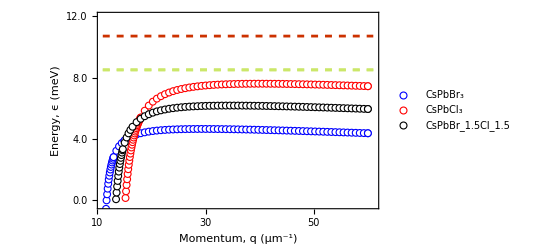

```mathematica
FinalDispersions = Show[s1,s2,s3, ClLT, BothLT, BrLT]
```

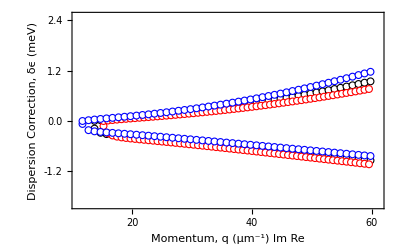

```mathematica
FinalCorrections = Show[qversusreal3, qversusimaginary3, qversusreal2, qversusimaginary2, qversusreal1, qversusimaginary1]
```